# Resonance

#### The objectives of the present notebook are: 1) Reviewing the different forms of resonances. 2) Identifying the relevant parameters for interpreting resonance phenomenon.

## 1. Dynamical Systems

#### How are dynamical systems mathematically formulated? What variables are traditionally utilized in order to describe their dynamics?

** Note that the present section will strictly focus on the classical  interpretation and will not dive into the Quantum derivation of dynamical systems.

### Quantifying Oscillator Systems

```mathematica
δ = 0.00; (*Damping Constant*)
ω0 = 0.00; (*Natural Frequency*)
 Α = 0.00; (*Amplitude*)
β = 0.00 ;(*Experimental Constant*)
Ρ = 0.00;  (*Phase*)
λ = 0.00; (*Damping Decay Rate*)

ϝ= ω0 / 2*Pi; (*Number of cycles / time unit = Hertz*)
τ = 1 / λ; (*Time constant = The time necessary for A to decrease by a factor of E (Euler's Number)*)
ϛ = λ / Sqrt[λ^2 + ω0^2]; (*Damping Ratio = Relation between the rate of decay and the natural frequency*)
𝒬 = 1 / (2 * ϛ); (*Q Factor = Representation of the amount of damping. High Q is interpreted as slow damping relative to the oscillation.*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

#### Natural Frequency ω0

The natural frequency of a system describe the oscillating behavior exhibited by a dynamical object.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ ω0*x[t] == 0,

(*Initial Conditions*)
x[0] == 1, 
x'[0] == 0},

x[t],

{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{ω0, 0,"Natural Frequency ω0"},0, 5}]
```

As you can observe, increasing the natural frequency of our pendulum will result to an increase in the number of cycle per second the system exhibit. Since no damping term is present, the oscillations do not decay overtime. 

Experimental example of natural frequency (ω0):
-

#### Damping δ

Damping describe the decay of oscillation amplitude over time. 

Relating to the natural frequency with damping:

δ = 0 --> Undamped System
δ < ω0 --> Underdamped System
δ = ω0 --> Critically Damped System
δ > ω0 --> Overdamped

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+δ*x'[t]+ ω0*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{ω0,0,"Natural Frequency -> ω0"},5.00, 15.00},
{{δ, 0,"Underdamped -> (δ < ω0)"},0.01, 3.99},
{{δ, 0,"Critically Damped -> (δ = ω0)"},5.00, 15.00},
{{δ, 0,"Over Damped -> (δ > ω0)"}, 15.01,50.00}]
```

RATE λ of DECAY:

```mathematica
Manipulate[

Plot[
{Α*E^(-λ*t)*Cos[ω0*t+Ρ]},
{t, 0, 10},
PlotRange->All,
PlotStyle->Red],

{{Α,0,"Amplitude -> Α"},0.00, 1.00},
{{ω0, 0,"Frequency -> ω0"},0.00, 50.00},
{{Ρ, 0,"Phase -> Ρ "},0.00, 5.00},
{{λ, 0,"Decay Rate -> λ "},0.00, 5.00}]
```

The DAMPING RATIO appears as a commonly used parameters describing the damping behavior exhibited by a system :
      
ζ = 0 -- > Undamped (Oscillations occur indefinitely with a constant amplitude over time)
ζ < 1 -- > Underdamped (Oscillations slowly decrease over time where the system is found to exhibit overshoot behavior until equilibrium is reached.)
ζ = 1 -- > Critically damped (
ζ > 1 -- > Overdamped (Oscillations rapidly decrease and eventually reach a rest position without ever over shooting. Note that the complete absence of oscillation is a fundamental limit of quantum mechanics. Nature appears to be incapable of reaching such as state where dynamical oscillations are absent.)

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+(2*ϛ*ω0)*x'[t]+ ω0^2*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{ω0,0,"Natural Frequency -> ω0"},0.00, 15.00},
{{ϛ, 0,"Underdamped -> ϛ < 1"},0.00, 0.99},
{{ϛ, 0,"Critically Damped -> ϛ = 1"},1.00, 1.00},
{{ϛ, 0,"Over Damped -> ϛ > 1"},1.001, 5.00}]
```

Increasing the amount of damping within the system will consequently leads to an incremental decrease of the natural frequency amplitude over time. 

Experimental example of damping (δ):
- Viscous Drag.
- Heat Dissipation.

#### Oscillating Spring Example

```mathematica
κ  = 0.00; (*Experimental stifness constant of the spring*)
𝓂 = 0.00; (*Mass value attached to the end of the spring*)
```

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+(κ/𝓂)*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{κ , 1, 5},
{𝓂 , 1, 10}]
```

As expected, the frequency of oscillation becomes lower as the mass value associated with the object attached to the spring becomes larger than the stiffness constant. Oppositely, if the mass of the object is very small compared with the stiffness constant, the frequency of oscillation is increase dramatically. 

The present example demonstrate how the natural frequency of a system can be adjusted experimentally. For the present case, the selection of an object with a specific mass as well as a spring with a desired stiffness constant will leads to a predictable natural frequency. As you might expect, a damping term would need to be added in order to represent a realistic version of an experiment. If no external energy is provided to the oscillating spring, the oscillation frequency will slowly decay over time.

### Having now gained some perspectives on how dynamical systems are mathematically represented, you can imagine the possibilities of observing various types of oscillator systems. We will explore below some known oscillator systems with peculiar properties.

### Pendulum Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+δ*x'[t] + Sin[x[t]] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5}]
```

#### Pendulum Oscillator Potential Energy

```mathematica
Clear[x]
```

```mathematica
Manipulate[

Plot[-Cos[x], 
{x, -5, 5},
PlotStyle->Red],
{x, -5, 5}]
```

#### Phase Space Representation (Angular Velocity (vs) Angle Position)

A phase space representation of a dynamical system allow to

```mathematica
Clear[x]
Clear[y]
```

```mathematica
v = NDSolve[

{x'[t] == 0.1*x[t]+y[t], 
y'[t] == -x[t]+0.1*y[t], 
x[0] == 0.01,
y[0] == 0}, 

{x[t], y[t]},

{t, 0, 50}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

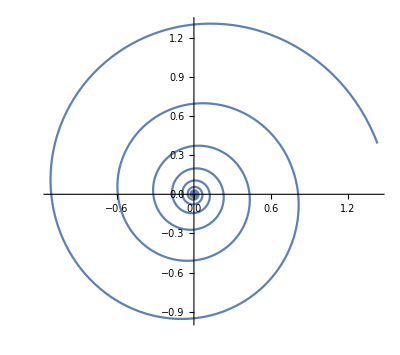

```mathematica
ParametricPlot[

{x[t], y[t]}/.v, 

{t, 0, 50}, 
PlotRange->All,
PlotPoints->1000]
```

#### Experimental Examples of Pendulum Oscillators

### Van Der pol Oscillator (Non-Linear Damping)

The peculiarity of the Van Der pol Oscillator arises from the NON-LINEAR DAMPING.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]- β*(1-x[t]^2)*x'[t]+  ω0^2*x[t] == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{β, 0, 5},
{ω0, 0, 5}]
```

#### Van Der Pol Oscillator Potential Energy

#### Phase Space Representation

#### Experimental Examples of Van Der pol Oscillators

### Morse Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t] + β*E^(-x[t])*(1-E^(-x[t])) == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5},
{β, 0, 5}]
```

#### Morse Oscillator Potential Energy

```mathematica
Manipulate[

Plot[
p[x] = 1/2*β*E^(-x)*(E^(-x)-2),
{x, -1,4},
PlotStyle->Red],
{β, 0, 1}]
```

#### Phase Space Representation

#### Experimental Examples of Morse Oscillator

### Jerk Oscillator (Third Derivative Term)

```mathematica
Manipulate[

sol = NDSolve[
{x'''[t]+ δ *x''[t]+ β*x'[t] + ω0^2*x[t]== 0,
x[0] == 1, 
x'[0] == 0,
x''[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 1, 5},
{β, 1, 5},
{ω0, 1, 5}]
```

#### Jerk Oscillator Potential Energy

#### Phase Space Representation

#### Experimental Examples of Jerk Oscillator

### Duffin Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5},
{ω0, 0, 5},
{β, 0, 5}]
```

#### Duffin Oscillator Potential Energy

```mathematica
Manipulate[

Plot[
p[x] = 1/2*ω0^2*x^2+1/4*β*x^4,
{x, -5,5},
PlotStyle->Red],

{ω0, -5,5},
{β, -5, 5}]
```

#### Phase Space Representation

#### Experimental Examples of Duffin Oscillators

### Quintic Oscillator

```mathematica
ν = 0.00;
```

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 + ν*x[t]^5== 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{δ, 0, 5},
{ω0, 0, 5},
{β, 0, 5},
{ν, 0, 5}]
```

#### Quintic Oscillator Potential Energy

```mathematica
Manipulate[

Plot[
p[x] = 1/2*ω0^2*x^2+1/4*β*x^4+ 1/6*ν*x^6,
{x, -5,5},
PlotStyle->Red],

{ω0, -5,5},
{β, -5, 5},
{ν, -5, 5}]
```

#### Phase Space Representation

#### Experimental Examples of Quintic Oscillators

## 2. External Forces & Resonant Responses

#### How are external forces mathematically formulated? What parameters are of interest in order for non-linear resonance to occur?

Oscillator Variables Definition:

```mathematica
δ = 0.00; (* Damping Constant *)
ω0 = 0.00; (* Natural Frequency *)
β = 0.00 ;(* Experimental Constant *)
 Α = 0.00; (*Amplitude*)
```

Force Variables Definition:

```mathematica
ωf = 0.00; (* Applied Force Frequency *)
af = 0.00 ;(* Applied Force Amplitude *)
```

#### Frequency Response Analysis

```mathematica
S = (ω0^2 - ωf^2)^2+ δ^2*ωf^2; 

Q = 1 / Sqrt[S]; (*Response Amplitude - Also defined as:  Q= Α/ωf*)

ωfMax= Sqrt[ω0^2-(δ^2/2)]; (*wfMax = Force frequency inducing a maximum response by the system*)

freqForceMax[ω0_, δ_]:= Sqrt[ω0^2-(δ^2/2)] (*Function allowing to derive the force frequency inducing a maximum amplitude response*)
```

Frequency Response Curve Example:

```mathematica
Clear[ω0, ωf, δ]
```

```mathematica
Manipulate[

Plot[
1 / Sqrt[(ω0^2 - ωf^2)^2+ δ^2*ωf^2],
{ωf, 0, 3},
PlotRange->All,
PlotStyle->Red,
AxesLabel-> {"Force Frequency ωf", "Amplitude Response Q"}],

{{δ,0,"Damping -> δ"},0.00, 3.0},
{{ω0,1,"Natural Frequency -> ω0 = 1"},1.00, 1.00}]
```

The frequency response curve below demonstrate the effect of damping on the response amplitude. 

Beyond a certain threshold of damping value, resonance becomes impossible. Specifically:

- δ > Sqrt[2*ω0^2] --> NO RESONANCE
- δ < Sqrt[2*ω0^2] --> RESONANCE BECOMES POSSIBLE
- Force Frequency inducing a maximum response amplitude = Sqrt[ω0^2-(δ^2/2)]

As shown below, as damping value increases, the required force frequency to induce a maximum amplitude decreases.

```mathematica
Manipulate[
freqForceMax[1, Damping],
{Damping, 0, 0.5}]
```

#### Resonance in Duffing Oscillator System

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == af*Cos[ωf*t],
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},
{{af, 0,"Force Amplitude -> af "},0,  5},
{{ωf, 0,"Force Frequency -> ωf "},0,  5}]
```

## 3. Stochastic Resonance

#### Stochastic resonance occurs when the addition of external noise reach a specific threshold and induce a maximum amplitude response by the dynamical system. Our intuition often assumes that noise leads to performance lost. Stochastic resonance prove the contrary.

#### Stochastic Resonance in Duffing Oscillator

Duffing Potential

```mathematica
Manipulate[

Plot[
1/2*ω0^2*x^2+1/4*β*x^4,
{x, -2, 2}],

{{ω0, -1,"Natural Frequency --> ω0"}, -5, 5},
{{β, -0.5,"Stiffness --> β"}, -2, 2}]
```

The command below was gathered from --> https : // demonstrations.wolfram.com/StochasticResonance/

```mathematica
Manipulate[

Module[{X, iX, evolPlot, tevolPlot,potentialPlot},
X=RecurrenceTable[
{x[n+1]== x[n] +dX[x[n],n * h, h, n,ϵ], 
x[1]==-1},x,
{n, 1, nsteps}];
iX=Table[{X⟦i⟧, h i}, {i, Length[X]}];

evolPlot=ListPlot[{iX,iTX.DiagonalMatrix[{ϵ, 1}]},
FrameLabel->{"X(t)", "t"},
Frame->True,
Joined->True, 
AspectRatio->1/2,
PlotRange->{{-1.2, 1.2}, {0, T}}, 
DataRange->{0, T},
PlotStyle->{Thickness[0.005]}];

potentialPlot=Plot[U[x, t,ϵ], {x, -1.2, 1.2}, 
FrameLabel->{"X", "U(x)"},
PlotRange->{-0.7, 1.2}, 
PlotStyle->{RGBColor[0.7, 0.7, 1.0],Thickness[0.02]},
AspectRatio->1/2,
Frame->True, 
Epilog->{RGBColor[0.1, 0, 0.4], PointSize[0.05], Point[{X⟦1+Floor[t/h]⟧, U[X⟦1+Floor[t/h]⟧, t,ϵ]}]}];

GraphicsColumn[
{potentialPlot,Show[evolPlot, Epilog->{Red,Opacity[0.5],Rectangle[{-1.0, t-200 h/2}, {1.0, t+200 h/2}]}]}, 
Automatic,
ImageSize->450,
AspectRatio->1/2,
Spacings->{0,0}]],

{{ϵ,0.3, "Force Amplitude"}, 0, 0.5},
{{η, 0.1, "Noise Level"}, 0, 1.0, 0.1},
{{t, 0, "Time"}, 0,400-.01},

TrackedSymbols->True,
SynchronousUpdating->False,

Initialization:>(
Clear[x];

(* The period of the time-dependent forcing *)
τ=100;

(* Time step *)
h=0.1; 

(* Total simulated time. *)
T=400;

nsteps=Floor[T/h];

(* To save time, we build a table of normally distributed random values *)
normal=RandomReal[NormalDistribution[0,1],nsteps];

(* The time-independent part of the potential (a bi-stable potential)*)
U0[x_]:=x^4-x^2;

(* The time-dependent forcing *)
v[x_, t_]:=Cos[2 π t/τ] x;

TX=Sin[2 π Range[1, nsteps] h/τ];
iTX=Table[{TX⟦i⟧, h i}, {i, Length[TX]}];
U[x_, t_,ϵ_]=U0[x]+ϵ v[x, t];
F[x_, t_,ϵ_]=-D[U[x, t,ϵ], x];
dX[x_, t_, dt_, n_Integer,ϵ_]:=dt F[x, t,ϵ] +η Sqrt[h] normal⟦n⟧;
)]
```

As demonstrated in the above simulation, when the noise value crosses a threshold, the system is forced to oscillate from one potential well to another.

## 4. Vibrational Resonance

#### Vibrational resonance occurs when the noise term from stochastic resonance is replaced by a high frequency force.

#### Vibrational Resonance in Duffing Oscillator

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == af*Cos[ωfa*t] + bf* Cos[ωfb*t],
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},

(*External Force Parameters*)

{{af, 0,"Force Amplitude A-> af "},0,  5},
{{bf, 0,"Force Amplitude B-> bf "},0,  5},
{{ωfa, 0,"Force Frequency A -> ωfa "},0,  5},
{{ωfb, 0,"Force Frequency B -> ωfb "},0,  5}]
```

## 5. Coherence Resonance

#### Coherence resonance occurs when a system is stimulated only by an external white noise.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*x[t] + β*x[t]^3 == 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},
{{β, 0,"Stiffness Constant -> β "},0,  5},

(*External Force Parameters*)

{{af, 0,"Force Amplitude A-> af "},0,  5},
{{bf, 0,"Force Amplitude B-> bf "},0,  5},
{{ωfa, 0,"Force Frequency A -> ωfa "},0,  5},
{{ωfb, 0,"Force Frequency B -> ωfb "},0,  5}]
```

## 6. Ghost Resonance

#### Ghost resonance occurs when a force frequency induces a resonant response at a frequency that is absent from the external stimulus. (p.263)

```mathematica
δ = 0.00; (*Damping Constant*)
ω0 = 0.00; (*Natural Frequency*)
 Α = 0.00; (*Amplitude*)
β = 0.00 ;(*Experimental Constant*)
Ρ = 0.00;  (*Phase*)
λ = 0.00; (*Damping Decay Rate*)

ωf = 0.00; (* Applied Force Frequency *)
af = 0.00 (* Applied Force Amplitude *)

fi = (k+n-1)*ω0;
F = (Α/n) Sum[Sin[2*Pi*fi*t], {1, n}];
```

0.

Sum::itraw: Raw object 1 cannot be used as an iterator.

Sum::vloc: The variable 1 cannot be localized so that it can be assigned to numerical values.

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+a * x[t]+β*x[t]^3== F + af*Cos[ωf*t],
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 1,"Damping -> δ "},1, 50},
{{a, 1,"Experimental Variable -> a"},1, 50},
{{β, 1,"Experimental Variable -> β "},1,  50},

(*External Forces*)
{{Α, 1,"Positive Integer -> Α "},1,  50},
{{n, 1,"Positive Integer -> n "},1,  50},
{{k, 1,"Positive Integer -> k "},1,  50},
{{ω0, 1,"Positive Integer -> ω0 "},1,  50},
{{af, 1,"Positive Integer -> af "},1,  50},
{{ωf, 1,"Positive Integer -> wf "},1,  50}]
```

## 7. Parametric Resonance

#### As opposed to the other forms of non-linear resonances previously analyzed, parametric resonance occurs from a variation of the parameters defining the system. For instance, a constant change of natural frequency would induce a maximum amplitude response.

```mathematica
Clear[δ , ω0, Α]
```

```mathematica
δ = 0.00; (*Damping Constant*)
ω0 = 0.00; (*Natural Frequency*)
 Α = 0.00; (*Amplitude*)
β = 0.00 ;(*Experimental Constant*)
Ρ = 0.00;  (*Phase*)
λ = 0.00; (*Damping Decay Rate*)
```

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*(1+ Α*Cos[(2*ω0/n)*t]) *x[t]== 0,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0,"Damping -> δ "},0, 50},
{{ω0, 0,"Natural Frequency -> ω0"},0, 50},
{{n, 1,"Positive Integer -> n "},1,  50},
{{Α, 0,"Positive Integer -> Α "},0,  50}]
```

## 8. AutoResonance

P. 306

```mathematica
Manipulate[

sol = NDSolve[
{x''[t]+ δ*x'[t]+ω0^2*Sin[x[t]] == af*Cos[(ω0*t - a*t^2)/2] ,
x[0] == 1, 
x'[0] == 0},
x[t],
{t, 0, 1000}];

Plot[
Evaluate[
x[t] /. sol],
{t, 0, 100},
PlotRange->All,
PlotStyle->Red],

{{δ, 0,"Damping -> δ "},0, 5},
{{ω0, 0,"Natural Frequency -> ω0"},0, 5},

(*External Force Parameters*)

{{af, 0,"Force Amplitude af-> af "},0,  5},
{{a, 0,"Force Amplitude a-> a "},0,  5}]
```

## 9. Chua’s Circuit as a Non-Linear Oscillator

### Chua’s Phase Space

```mathematica
(* The simulation below
```

```mathematica
(*Components Values*)
```

```mathematica
R = 2500;
C1 = 10*10^-9;
C2 = 100*10^-9;
L = 0.375;
```

```mathematica
(* Chua's Diode Parameters *)
```

```mathematica
m0 = -1.1;
m1 = -0.7;
```

```mathematica
coil=ParametricPlot[{1.5*Cos[2*t],t+1.5*Sin[2*t]},{t,0,4*Pi},PlotStyle->Black];
l1=Graphics[{Thick,Line[{{1.5,0},{1.5,-2},{10,-2}}]}];
l2=Graphics[{Thick,Line[{{1.5,4*Pi},{1.5,15},{12,15}}]}];
vl2=Graphics[{Thick,Line[{{10,15},{10,6.5}}]}];
vl2a=Graphics[{Thick,Line[{{10,6},{10,-2}}]}];
hl2=Graphics[{Thick,Line[{{9.0,6.5},{11.0,6.5}}]}];
hl2a=Graphics[{Thick,Line[{{9.0,6.0},{11.0,6.0}}]}];
resistor=Graphics[{Thick,Line[Table[{12+i 2/(4 3),15+3/3 Sin[i Pi/2]},{i,0,4 3}]]}];
vl3=Graphics[{Thick,Line[{{17,15},{17,6.5}}]}];
vl3a=Graphics[{Thick,Line[{{17,6},{17,-2}}]}];
hl3=Graphics[{Thick,Line[{{16.0,6.5},{18.0,6.5}}]}];
hl3a=Graphics[{Thick,Line[{{16.0,6.0},{18.0,6.0}}]}];
l4=Graphics[{Thick,Line[{{10,-2},{25,-2},{25,3.5}}]}];
l5=Graphics[{Thick,Line[{{14,15},{25,15},{25,11}}]}];

sawline=Graphics[{Thick,Line[Table[{25+(-1)^n,n/2+5},{n,10}]]}];ddb=Graphics[{Thick,Line[{{24,5.5},{25,5.25},{25,4.5}}]}];rectangle=Graphics[Rectangle[{23.5,4.5},{26.5,3.5}]];ddp=Graphics[{Thick,Line[{{26,10},{25,10.25},{25,11}}]}];box=Graphics[{Thick,Line[{{26.5,3.5},{26.5,11},{23.5,11},{23.5,3.5}}]}];ax=Graphics[{Arrowheads[Large],Arrow[{{3,15},{7,15}}]}];ax1=Graphics[{Arrowheads[Large],Arrow[{{17,15},{22,15}}]}];a0=Graphics[Text[Style[""],{5,16}]]; 
a1=Graphics[Text[Style["L",FontSize->14],{2.6,6.25}]]; 
a2=Graphics[Text[Style["R=1/G",FontSize->14],{14.0,17.25}]]; 
a3=Graphics[Text[Style[""],{20.6,16.5}]]; 
a4=Graphics[Text[Style["+",FontSize->14],{26,12.25}]]; 
a5=Graphics[Text[Style["-",FontSize->14],{26,2.25}]]; 
a6=Graphics[Text[Style[""],{28.6,6.5}]]; 
c1=Graphics[Text[Style[""],{14.6,6.5}]]; 
c2=Graphics[Text[Style[""],{7.5,6.5}]]; 
v1=Graphics[Text[Style[""],{18.5,7.5}]]; 
v2=Graphics[Text[Style[""],{11.5,7.5}]]; 
v3=Graphics[Text[Style[""],{28.0,10.5}]]; 
Show[l1,l2,coil,vl2,vl2a,hl2,hl2a,resistor,vl3,vl3a,hl3,hl3a,l4,l5,sawline,ddb,rectangle,ddp,box,ax,ax1,a0,a1,a2,a3,a4,a5,a6,c1,c2,v1,v2,v3]
```

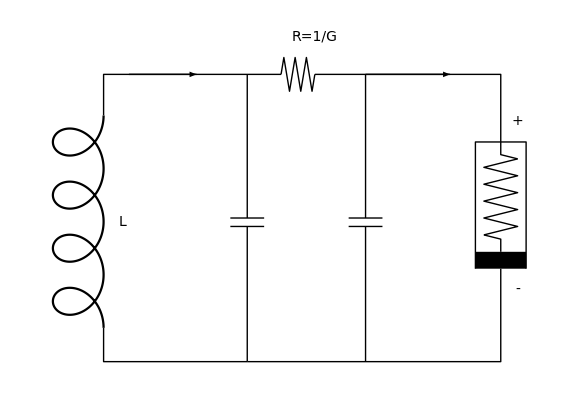

```mathematica
Manipulate[
Module[{
sol={v,i,x}/.Quiet[NDSolve[{

v'[t]==i[t]/CC,

i'[t]==-1/L(v[t]+
Switch[memristanceChoices,

1,β( x[t]^2 -1),
2,-β x[t],
3,β x[t]]*i[t]),

x'[t]==Switch[internalStateChoices,

1,-i[t]-α x[t]+i[t]*x[t],
2,1-i[t]^2,
3,2/7 i[t]-3/14(Abs[i[t]+1]-Abs[i[t]-1])],

v[0]==v0,
i[0]==i0,
x[0]==x0},

{v,i,x},
{t,0,tmax},
MaxSteps->Infinity]][[1]]},

Grid[{{Text@Style["2D phase portrait, time domain waveform, and a 3D phase portrait",Bold],SpanFromLeft,SpanFromLeft},
{ParametricPlot[{First[sol][t],First[Rest[sol]][t]},{t,0,tmax},AxesLabel->{v[t],i[t]},ImageSize->{180,180},AspectRatio->1,PlotRange->All,MaxRecursion->8,PerformanceGoal->8,ImagePadding->25],Plot[First[sol][t],{t,0,tmax},AxesLabel->{t,v[t]},ImageSize->{150,150},PlotRange->All,MaxRecursion->8,PerformanceGoal->8,ImagePadding->20]},
{ParametricPlot3D[{First[sol][t],First[Rest[sol]][t],Last[sol][t]},{t,0,tmax},AxesLabel->{v,i,x},ImageSize->{180,180},BoxRatios->{1,1,1},PlotRange->Full,MaxRecursion->8,PerformanceGoal->8,ColorFunction->"Rainbow",ImagePadding->20],SpanFromLeft}}]],Style["system parameters",Bold],

(* Memristance and Internal State Functions *)
{{memristanceChoices, 1, "memristance"},{
1->"β (x^2 - 1)",
2->"- β x",
3->"β x"},
ControlType->PopupMenu,
ControlPlacement->Top},

{{internalStateChoices, 1, "internal state function"},{
1->"- i - α x + i x",
2->"1 - i^2",
3->"2/7 i - 3/14 (|i + 1} - |i - 1})"},
ControlType->PopupMenu,
ControlPlacement->Top},


{{β,1.5,"β"},1,3,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{α,0.6,"α"},0.1,3,0.1,Enabled:>memristanceChoices===1,Appearance->"Labeled",ImageSize->Tiny},

(* Circuit Parameters and Simulation Time *)
{{CC,1,"C"},1,3,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{L,3,"L"},1,5,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{tmax,500,"t"},0.1,1000,0.1,Appearance->"Labeled",ImageSize->Tiny},

(* Initial Conditions *)
{{v0,0.1,"v_0"},-1,1,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{i0,0,"i_0"},-1,1,0.1,Appearance->"Labeled",ImageSize->Tiny},
{{x0,0.1,"x_0"},-1,1,0.1,Appearance->"Labeled",ImageSize->Tiny},
SynchronousUpdating->False,ControlPlacement->Left,AutorunSequencing->{1,3,5,7},TrackedSymbols->True]
```